NIntegrate::inumr: The integrand Log[Tanh[(x+ⅈ π y) √(1.49-1.4 Cos[«1»])] Tanh[(Conjugate[x]-ⅈ π Conjugate[y]) √(1.49-1.4 Cos[«1»])]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

ContourPlot::exclul: {Cosh[(Conjugate[x]-ⅈ π Conjugate[y]) √(1.49-1.4 Cos[«1»])]-0,Cosh[(x+ⅈ π y) √(1.49-1.4 Cos[«1»])]-0,Im[Tanh[(x+Times[«3»]) √Plus[«2»]] Tanh[(Conjugate[«1»]+Times[«3»]) √Plus[«2»]]]-0} must be a list of equalities or real-valued functions.

NIntegrate::inumr: The integrand Log[Tanh[(x+ⅈ π y) √(1.49-1.4 Cos[«1»])] Tanh[(Conjugate[x]-ⅈ π Conjugate[y]) √(1.49-1.4 Cos[«1»])]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

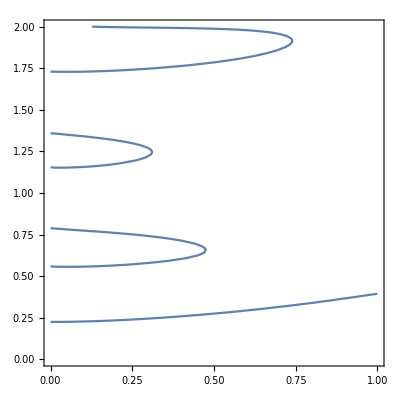

```mathematica
Clear[g];Clear[energy,Zexact];
energy=√(1+g^2-2g*Cos[q]);g=0.7;
Zexact[β_]:=NIntegrate[Log[Tanh[β*energy]*Tanh[Conjugate[β]*energy]],{q,0,π},WorkingPrecision->10];
ContourPlot[Re[Zexact[x+I*y*π]]==0,{x,0,1},{y,0,2}]
```